```mathematica
square = Rectangle[{-1,-1},{1,1}];
(* square = Rectangle[]; *)
boundary=RegionBoundary[square]⟦1⟧;
nodes=Most@boundary;
n=Length@nodes;
ListPlot[
nodes,
LabelingFunction->(Position[nodes,#]&),
AspectRatio->1,PlotStyle->{PointSize->Large},ImageSize->Small
];
```

```mathematica
standardBasisFunctions={
1&,
#⟦1⟧&,
#⟦2⟧&,
#⟦1⟧#⟦2⟧&
};
H=Table[standardBasisFunctions⟦j⟧[nodes⟦i⟧],{i,1,n},{j,1,n}];
Subscript[H, inv]=Inverse@H;
Subscript[H^T, inv]=Transpose@Subscript[H, inv];
```

```mathematica
Ψ=Table[
With[{i=i},Sum[Subscript[H^T, inv]⟦i,j⟧standardBasisFunctions⟦j⟧@#,{j,1,n}]&],{i,1,n}];
Simplify[Through[Ψ[{ξ,η}]]]// MatrixForm;
```

```mathematica
(* NIntegrate is bad in our case since it does a lot of unnecessary work *) (* We know that we are using polynomials => quick exact gaussian quadrature formulas *)
locWeights=N@{{{-1/(√3),-1/(√3)},1},{{1/(√3),-1/(√3)},1},{{-1/(√3),1/(√3)},1},{{1/(√3),1/(√3)},1}};
numericIntegrate[fSymb_]:=Sum[locWeights⟦i,2⟧(fSymb/.{ξ->locWeights⟦i,1,1⟧,η->locWeights⟦i,1,2⟧}),{i,1,Length@locWeights}]
```

```mathematica
(* The list of shape functions and its gradient when evaluated at ξ and η *)
ψ=Simplify@{Through[Ψ[{ξ,η}]]};
ψT=Transpose@ψ;
ψTψ=Simplify[ψT.ψ];
gradψ=Transpose@Grad[Through[Ψ[{ξ,η}]],{ξ,η}];
gradψT=Transpose@gradψ;

J[elementNodes_?MatrixQ]:=gradψ.elementNodes
(* By taking B=|J| J^-1 we end up calculating |J|/inverse once less in the integral and can directly provide formula for the values *)
B[elementNodes_?MatrixQ]:=Module[{j=J@elementNodes},
{{j⟦2,2⟧,-j⟦1,2⟧},
{-j⟦2,1⟧,j⟦1,1⟧}}
]
(* Alternatively - we may just calculate B for a given Jacobian, since we will have to calculate it in the stiffness anyway *)
BfromJ[j_?MatrixQ]:={{j⟦2,2⟧,-j⟦1,2⟧},{-j⟦2,1⟧,j⟦1,1⟧}}
```

```mathematica
localMass[elementNodes_?MatrixQ]:=numericIntegrate[Abs@Det@J[elementNodes] ψT.ψ]
localStiffness[elementNodes_?MatrixQ]:=Module[{j=J@elementNodes,b,bT,f},
b=BfromJ@j;
bT=Transpose@b;
numericIntegrate[1/(Abs@Det@j)gradψT.bT.b.gradψ ]
]
```

```mathematica
FEMMatrix[nodes_?ListQ,elements_?ListQ,localFunction_,nullNodes_:{}?ListQ]:=Module[{
globalMatrix = SparseArray@ConstantArray[0,{Length@nodes,Length@nodes}], element, quality},
For[k=1,k≤Length@elements,k++,
element = elements⟦k⟧;
quality=localFunction@nodes⟦element⟧;
For[i=1,i≤Length@element,i++,
For[j=1,j≤Length@element,j++,
globalMatrix⟦element⟦i⟧,element⟦j⟧⟧+=quality⟦i, j⟧;
];
];
];

(* We should now take into account that some of the coefficients will have to be 0 to ensure the boundary condition of u=0 *)
For[i=1,i≤Length@nullNodes,i++,
For[j=1,j≤Length@nodes,j++,
globalMatrix⟦j,nullNodes⟦i⟧⟧=0;
globalMatrix⟦nullNodes⟦i⟧,j⟧=0;
];
globalMatrix⟦nullNodes⟦i⟧,nullNodes⟦i⟧⟧=1;
];

globalMatrix
]

(* The function that assebles the global stiffness matrix *)
stiffnessMatrix[nodes_?ListQ,elements_?ListQ,nullNodes_?ListQ]:=FEMMatrix[nodes,elements,localStiffness,nullNodes]

(* The function that assebles the global mass matrix *)
massMatrix[nodes_?ListQ,elements_?ListQ,nullNodes_?ListQ]:=FEMMatrix[nodes,elements,localMass,nullNodes]
```

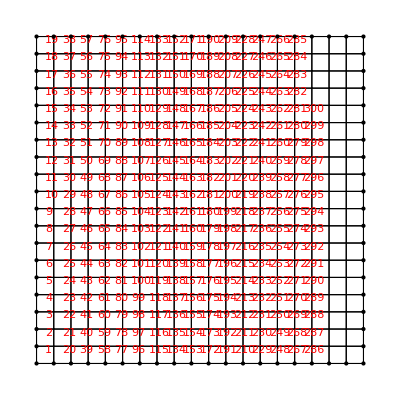

```mathematica
(* Discretization of the region *)
Ω=Rectangle[];
Needs["NDSolve`FEM`"]
mesh=ToElementMesh[Ω, "MeshOrder"-> 1,MaxCellMeasure->0.003];
mesh["Wireframe"];
Show[mesh["Wireframe"["MeshElementIDStyle"->Red]],mesh["Wireframe"["MeshElement"->"PointElements","MeshElementIDStyle"->Blue]]]
nodes = mesh["Coordinates"];
elements = mesh["MeshElements"]⟦1,1⟧;
boundary =Flatten[mesh["BoundaryElements"]⟦1,1⟧];
boundary=DeleteDuplicates[boundary];
```

```mathematica
Subscript[M, 0]=massMatrix[nodes,elements,{}];
Subscript[M, 1]=stiffnessMatrix[nodes,elements,{}];
```

```mathematica
initialU[{x_,y_}]:=If[x^2+y^2≤1/16,100,0]
α[u_]:=u
G[u_]:=u^2/2
```

```mathematica
nonStandardFEM[nodes_?ListQ,elements_?ListQ,nullNodes_?ListQ,T_,τ_,uInit_,α_,G_,M0_,M1_]:=Module[{
n=Length@nodes,m=Ceiling@(T/τ),Mconc,GVec,sol,jacobian,F,h,step=21,time,dt},
sol=ConstantArray[0,{m,n}];
sol⟦1⟧=uInit/@nodes;
time=0;
(* Concentrating the mass matrix allows a bit larger stable values of τ *)
Mconc=SparseArray@DiagonalMatrix[Table[Total@M0⟦i⟧,{i,1,n}]];

Monitor[For[j=1,j<m,j++,
dt=First@Timing[GVec=G/@sol⟦j⟧;
sol⟦j+1⟧=If[step>20,LinearSolve[Mconc,Mconc.sol⟦j⟧-τ M1.GVec],sol⟦j⟧];
step=1;
h=ConstantArray[1,n];
(* Use Newton's metod with analytically found Jacobian *)
While[h.h≥τ&&step≤20,
F=Mconc.(sol⟦j+1⟧-sol⟦j⟧)+τ/2 M1.(G/@sol⟦j+1⟧+GVec);
jacobian=Mconc+τ/2 M1.DiagonalMatrix[α/@sol⟦j+1⟧];
h=LinearSolve[jacobian,F];

sol⟦j+1⟧-=h;
step++;
];];

time+=dt;
];,Row[{ProgressIndicator[j,{1,m}],StringForm["``s",NumberForm[time,{100,3}]]}," "]];

sol
]
```

```mathematica
(* Solve the equation *)
T=0.05;
τ=0.5 10^-4;
{timeTaken,q}=Timing@nonStandardFEM[nodes,elements,{},T,τ,initialU,α,G,Subscript[M, 0],Subscript[M, 1]];
StringForm["FEM took ``s to approximate solution",NumberForm[timeTaken,{100,3}]]
u=Table[Interpolation[Thread[{nodes,q⟦k⟧}],InterpolationOrder->1],{k,1,Length@q}];
```

FEM took 12.328s to approximate solution

```mathematica
(* Contour plot of the interpolated solution *)
Manipulate[
ContourPlot[
{u⟦k⟧[x,y]},
{x,y}∈Ω,
PlotRange->All,ContourLabels->True,ColorFunction->"DarkRainbow",
PlotLabel->"Contour plot of u"],
{k,1,Length@u,1}
];
```

```mathematica
(* 3D plot of the interpolated solution *)
Manipulate[
Plot3D[
{u⟦k⟧[x,y]},
{x,y}∈Ω,
PlotLabel->"3D plot of u"],
{k,1,Length@u,1}
];
```

```mathematica
(* 3D list plot of the solution *)
Manipulate[
ListPlot3D[
MapThread[Append,{nodes,q⟦k⟧}],
PlotLabel->"3D plot of u"],
{k,1,Length@u,1}
];
```